1.86204×10^18 ⅇ^(-68.0782 (-0.296+xd)^2)

8.25967×10^19 ⅇ^(-214.326 (-0.114+xd)^2)

5.24924×10^20 ⅇ^(-2164.13 (-0.0362+xd)^2)

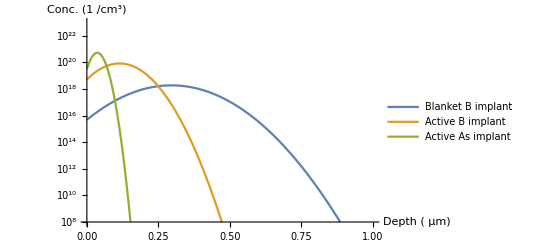

```mathematica
(* Ion implants *)
ConcProfile[xd_,Q_,RP_,dRP_,Dteff_]:=Q/(√(2π(dRP^2+2Dteff))) Exp[-(xd-RP)^2/(2(dRP^2+2Dteff))];
ProfileB1[xd_,Dteff_]=ConcProfile[xd,4*10^13*10^-8,0.296,0.0857,Dteff]*10^12;
ProfileB2[xd_,Dteff_]=ConcProfile[xd,1*10^15*10^-8,0.114,0.0483,Dteff]*10^12;
ProfileAs[xd_,Dteff_]=ConcProfile[xd,2*10^15*10^-8,0.0362,0.0152,Dteff]*10^12;
ProfileB1[xd,0]
ProfileB2[xd,0]
ProfileAs[xd,0]

LogPlot[{ProfileB1[xd,0],ProfileB2[xd,0],ProfileAs[xd,0]}, {xd,0,1},PlotRange->{10^8,10^23},AxesLabel-> {"Depth ( µm)","Conc. (1 /cm^3)"},PlotLegends->Placed[LineLegend[ {"Blanket B implant","Active B implant", "Active As implant"}],{0.75,0.8}],BaseStyle->{FontSize->14},LabelStyle->{FontSize->12}]
```

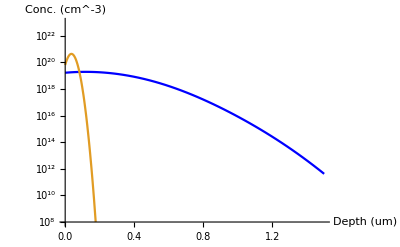

7.10632×10^17 ⅇ^(-9.91561 (-0.296+xd)^2)

1.87791×10^19 ⅇ^(-11.079 (-0.114+xd)^2)

4.32491×10^20 ⅇ^(-1469.07 (-0.0362+xd)^2)

2.98088×10^17

1.62609×10^19

6.30815×10^19

```mathematica
(* Diffusion steps *)
k=8.61733*10^-5;
D0B=1*10^8;
EAB=3.5;
D0As=9.17*10^8;
EAAs=3.99;
Dfunc[D0_,EA_,T_]:=D0 Exp[-EA/(k (T+273.15))];
Dteff1B1=Integrate[Dfunc[D0B,EAB,800+10t/60], {t,0,5*60}]+Dfunc[D0B,EAB,850]*20*60 + Integrate[Dfunc[D0B,EAB,850-10t/60], {t,0,5*60}];
Dteff1B1=Dteff1B1+Dfunc[D0B,EAB,785]*45*60 ;
Dteff1B1=Dteff1B1+Integrate[Dfunc[D0B,EAB,800+10t/60], {t,0,20*60}]+Dfunc[D0B,EAB,1000]*105*60 + Integrate[Dfunc[D0B,EAB,1000-10t/60], {t,0,20*60}];
Dteff1B1=Dteff1B1+Integrate[Dfunc[D0B,EAB,800+10t/60], {t,0,5*60}]+Dfunc[D0B,EAB,850]*15*60 + Integrate[Dfunc[D0B,EAB,850-10t/60], {t,0,5*60}];
Dteff1B1=Dteff1B1+Integrate[Dfunc[D0B,EAB,800+10t/60], {t,0,10*60}]+Dfunc[D0B,EAB,900]*20*60 + Integrate[Dfunc[D0B,EAB,900-10t/60], {t,0,10*60}];
Dteff2B1=Dteff1B1+Integrate[Dfunc[D0B,EAB,800+10t/60], {t,0,10*60}]+Dfunc[D0B,EAB,900]*20*60 + Integrate[Dfunc[D0B,EAB,900-10t/60], {t,0,10*60}];
DteffAs=Integrate[Dfunc[D0As,EAAs,800+10t/60], {t,0,10*60}]+Dfunc[D0As,EAAs,900]*20*60 + Integrate[Dfunc[D0As,EAAs,900-10t/60], {t,0,10*60}];

Dteff1B2=Integrate[Dfunc[D0B,EAB,800+10t/60], {t,0,20*60}]+Dfunc[D0B,EAB,1000]*105*60 + Integrate[Dfunc[D0B,EAB,1000-10t/60], {t,0,20*60}];
Dteff1B2=Dteff1B2+Integrate[Dfunc[D0B,EAB,800+10t/60], {t,0,5*60}]+Dfunc[D0B,EAB,850]*15*60 + Integrate[Dfunc[D0B,EAB,850-10t/60], {t,0,5*60}];
Dteff1B2=Dteff1B2+Integrate[Dfunc[D0B,EAB,800+10t/60], {t,0,10*60}]+Dfunc[D0B,EAB,900]*20*60 + Integrate[Dfunc[D0B,EAB,900-10t/60], {t,0,10*60}];
Dteff2B2=Dteff1B2+Integrate[Dfunc[D0B,EAB,800+10t/60], {t,0,10*60}]+Dfunc[D0B,EAB,900]*20*60 + Integrate[Dfunc[D0B,EAB,900-10t/60], {t,0,10*60}];
plot=LogPlot[{ProfileB1[xd,Dteff2B1]+ProfileB2[xd,Dteff2B2],ProfileAs[xd,DteffAs]}, {xd,0,1.5},PlotRange->{10^8,10^23},AxesLabel-> {"Depth (um)","Conc. (cm^-3)"},PlotStyle->{Blue,Normal}]
ProfileB1[xd,Dteff2B1]
ProfileB2[xd,Dteff2B2]
ProfileAs[xd,DteffAs]
ProfileB1[0,Dteff2B1]
ProfileB2[0,Dteff2B2]
ProfileAs[0,DteffAs]
```